```mathematica
ClearAll["Global`*"]
```

```mathematica
brg[pos_]:=ArcTan[pos[[2]],pos[[1]]]
trialvel[brg0_,brg1_,r0_,r1_,op0_,op1_,t_]:=1/t*(r1*{Sin[brg1],Cos[brg1]}-r0*{Sin[brg0],Cos[brg0]}+op1-op0)
trialpos[brg0_,brg1_,r0_,r1_,op0_,op1_,t_,totaltime_]:=r0*{Sin[brg0],Cos[brg0]}+t*trialvel[brg0,brg1,r0,r1,op0,op1,totaltime]
```

```mathematica
tp0 = {72/(√157),132/(√157)};
tv ={1/10 (12/(√13)-72/(√157)),1/10 (10-18/(√13)-132/(√157))};
ov0 = {0,1};
ov1 := Norm[ov0]*{Sin[secondcourse],Cos[secondcourse]};
totaltime =10;
timeofzig = 5;
secondcourse = brg[ov0];
```

```mathematica
ospos[t_]:=If[t<timeofzig,ov0*t,ov0*timeofzig+ov1*(t-timeofzig)];
targetpos[t_]:=tp0+t*tv;
brg0 = brg[tp0];
brg1=brg[targetpos[timeofzig]-ospos[timeofzig]];
brg2 = brg[targetpos[totaltime]-ospos[totaltime]];
```

```mathematica
Slider[Dynamic[r0],{0,20}]
Slider[Dynamic[r1],{0,20}]
r0=12
r1=6
(*r1:=r0/2;*)
Slider[Dynamic[secondcourse],{0,2π}]
Dynamic[ParametricPlot[{{brg[targetpos[t]-ospos[t]]*180/π,t},{brg[trialpos[brg0,brg[targetpos[totaltime]-ospos[totaltime]],r0,r1,ospos[0],ospos[totaltime],t,totaltime]-ospos[t]]*180/π,t}},{t,0,totaltime},PlotStyle->{Directive[Green,Thick],Directive[Red,Thin]},Ticks->{Range[-180,180,45],Range[0,10,2]},AxesLabel->{"True Bearing (°)","Time (Min)"},AxesStyle->White,AspectRatio->1,Background->Black]]
Dynamic[ParametricPlot[{ospos[t],targetpos[t],trialpos[brg0,brg[targetpos[totaltime]-ospos[totaltime]],r0,r1,ospos[0],ospos[totaltime],t,totaltime]},{t,0,totaltime},Axes->False]]
```

12

6

```mathematica
error[range0_,range1_,t_]:=(VectorAngle[targetpos[t]-ospos[t],trialpos[brg0,brg[targetpos[totaltime]-ospos[totaltime]],range0,range1,ospos[0],ospos[totaltime],t,totaltime]-ospos[t]])^2
errorsum[range0_,range1_,steps_]:=180./π*Sum[error[range0,range1,t],{t,0,totaltime,totaltime/steps}]/steps
```

```mathematica
rawcontour=ContourPlot[errorsum[range0,range1,20],{range0,.1,20},{range1,.1,20},PlotLegends->All,PlotLabel->"Cumulative Error (°-min) For Different Values of R1 and R2",FrameLabel->{"R1 (kyd)","R2 (kyd)"},ScalingFunctions->"Linear",PlotRange->All,Contours->Table[10^i,{i,2,-2,-.5}],ContourShading->Table[ColorData["MintColors"][i],{i,0,1,.11}],ImageSize->Large,LabelStyle->12];
```

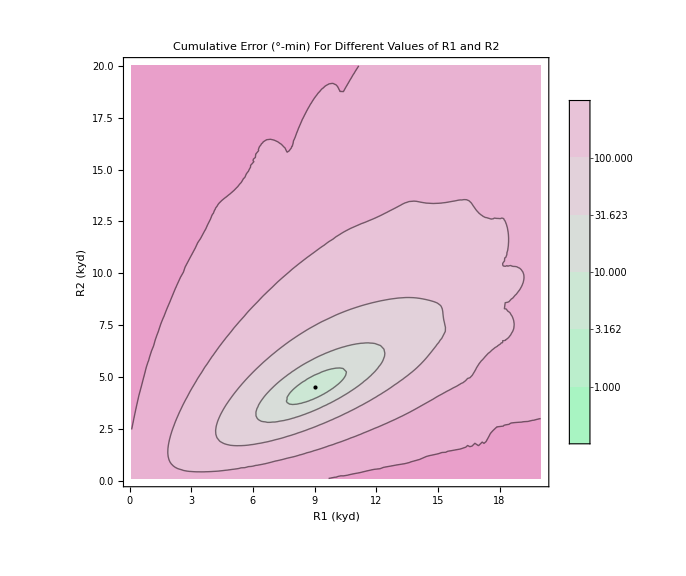

```mathematica
contour=Show[rawcontour,Graphics[Point[{r0,r1}]]]
```

```mathematica
{r0,r1}={9,4.5}
```

{9,4.5}

```mathematica
Export["contour2.png",contour]
```

contour2.png

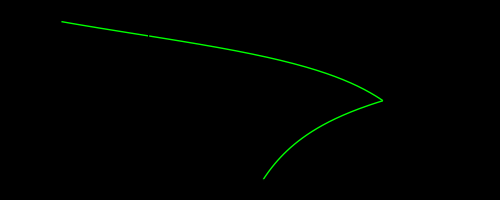

```mathematica
screen=ParametricPlot[{{brg[trialpos[brg0,brg[targetpos[totaltime]-ospos[totaltime]],r0,r1,ospos[0],ospos[totaltime],t,totaltime]-ospos[t]]*180/π,t}},{t,0,totaltime},PlotStyle->Directive[Green,Thick],Ticks->{Range[-180,180,45],Range[0,10,2]},AxesLabel->{"True Bearing (°)","Time (Min)"},AxesStyle->Directive[White,12],AspectRatio->Full,Background->Black]
```

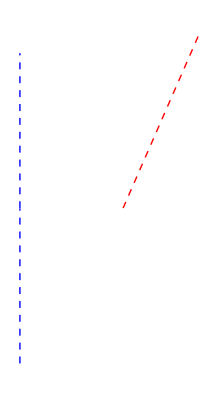

```mathematica
tracks = ParametricPlot[{ospos[t],trialpos[brg0,brg[targetpos[totaltime]-ospos[totaltime]],r0,r1,ospos[0],ospos[totaltime],t,totaltime]},{t,0,totaltime},Axes->False,PlotStyle->{Directive[Dashed,Blue,Thick],Directive[Dashed,Red,Thick]}]
```

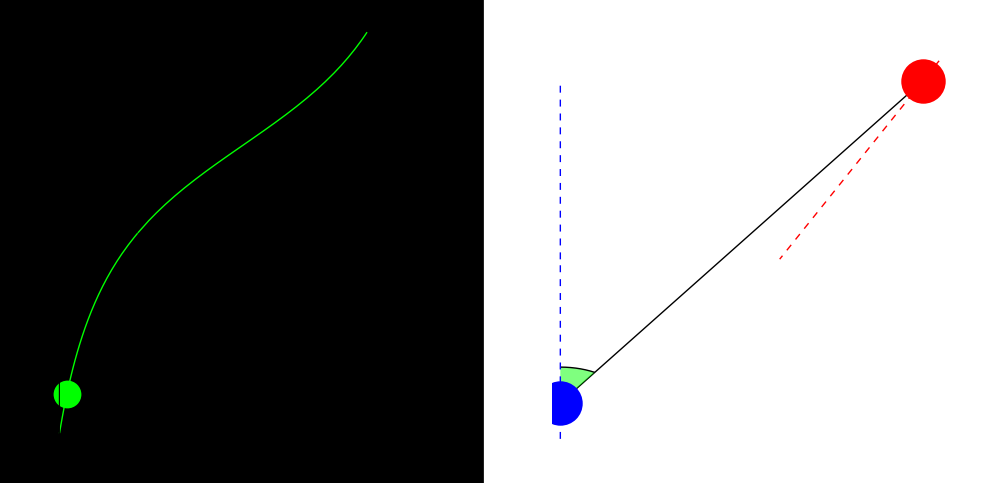

```mathematica
trackanimation[t_]:=GraphicsGrid[{{
Show[
screen,
Graphics[{
Green,
PointSize[.05],
Point[{brg[trialpos[brg0,brg[targetpos[totaltime]-ospos[totaltime]],r0,r1,ospos[0],ospos[totaltime],t,totaltime]-ospos[t]]*180/π,t}]
},ImageSize->Large]
],
Show[
Graphics[{
Line[{ospos[t],trialpos[brg0,brg[targetpos[totaltime]-ospos[totaltime]],r0,r1,ospos[0],ospos[totaltime],t,totaltime]}],
Opacity[.5],
Green,
Disk[ospos[t],1,{π/2,π/2-brg[trialpos[brg0,brg[targetpos[totaltime]-ospos[totaltime]],r0,r1,ospos[0],ospos[totaltime],t,totaltime]-ospos[t]]}],
Opacity[1],
Black,
Circle[ospos[t],1,{π/2,π/2-brg[trialpos[brg0,brg[targetpos[totaltime]-ospos[totaltime]],r0,r1,ospos[0],ospos[totaltime],t,totaltime]-ospos[t]]}],
PointSize[.08],
Blue,
Point[ospos[t]],
Red,
Point[trialpos[brg0,brg[targetpos[totaltime]-ospos[totaltime]],r0,r1,ospos[0],ospos[totaltime],t,totaltime]]
},PlotRange->{{0,6},{0,11}}],
tracks
]
}},ImageSize->1000]
trackanimation[1]
```

```mathematica
frames=Table[trackanimation[t],{t,0,10,.2}];
```

```mathematica
Export["onetrack.gif",frames,"AnimationRepetitions"->∞]
```

onetrack.gif

```mathematica
trialpos[brg0,brg[targetpos[totaltime]-ospos[totaltime]],r0,r1,ospos[0],ospos[totaltime],1,totaltime]-trialpos[brg0,brg[targetpos[totaltime]-ospos[totaltime]],r0,r1,ospos[0],ospos[totaltime],0,totaltime]
```

{1/10 (12/(√13)-72/(√157)),1/10 (10-18/(√13)-132/(√157))}

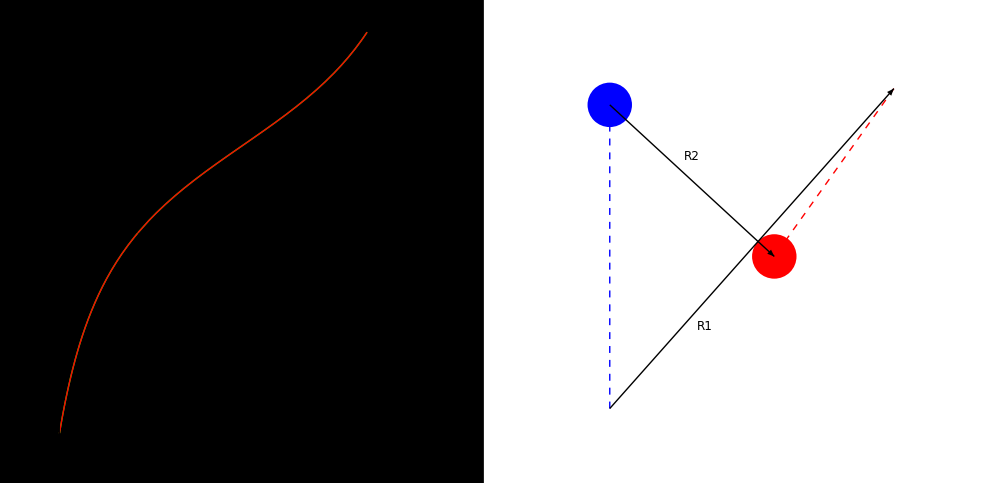

```mathematica
r1r2screen[vr0_,vr1_]:=ParametricPlot[{{brg[targetpos[t]-ospos[t]]*180/π,t},{brg[trialpos[brg0,brg[targetpos[totaltime]-ospos[totaltime]],vr0,vr1,ospos[0],ospos[totaltime],t,totaltime]-ospos[t]]*180/π,t}},{t,0,totaltime},PlotStyle->{Directive[Green,Thick],Directive[Red,Thin]},Ticks->{Range[-180,180,45],Range[0,10,2]},AxesLabel->{"True Bearing (°)","Time (Min)"},AxesStyle->Directive[White,12],AspectRatio->Full,Background->Black]
r1r2plot[vr0_,vr1_]:=Show[
ParametricPlot[{ospos[t],trialpos[brg0,brg[targetpos[totaltime]-ospos[totaltime]],vr0,vr1,ospos[0],ospos[totaltime],t,totaltime]},{t,0,totaltime},Axes->False,PlotStyle->{Directive[Dashed,Blue,Thick],Directive[Dashed,Red,Thick]},PlotRange->{{-1,7},{-1,12}}],
Graphics[{
PointSize[.08],
Blue,
Point[ospos[totaltime]],
Red,
Point[trialpos[brg0,brg[targetpos[totaltime]-ospos[totaltime]],vr0,vr1,ospos[0],ospos[totaltime],totaltime,totaltime]],
Black,
Arrowheads[{-Medium,Medium}],
Arrow[{ospos[0],trialpos[brg0,brg[targetpos[totaltime]-ospos[totaltime]],vr0,vr1,ospos[0],ospos[totaltime],0,totaltime]}],
Arrow[{ospos[totaltime],trialpos[brg0,brg[targetpos[totaltime]-ospos[totaltime]],vr0,vr1,ospos[0],ospos[totaltime],totaltime,totaltime]}],
Text[Style["R1",FontSize->12],(2*ospos[0]+trialpos[brg0,brg[targetpos[totaltime]-ospos[totaltime]],vr0,vr1,ospos[0],ospos[totaltime],0,totaltime])/3-{0,.8}],
Text[Style["R2",FontSize->12],(ospos[totaltime]+trialpos[brg0,brg[targetpos[totaltime]-ospos[totaltime]],vr0,vr1,ospos[0],ospos[totaltime],totaltime,totaltime])/2+{0,.8}]
},PlotRange->{{-1,7},{-1,12}}]
]
r1r2demo[{vr0_,vr1_}]:=GraphicsGrid[{{r1r2screen[vr0,vr1],r1r2plot[vr0,vr1]}},ImageSize->1000]
r1r2demo[{12,6}]
```

```mathematica
exampleranges=Join[
Table[{12-11*(Sin[t*π/20])^2,6},{t,0,20}],
Table[{12,6},5],
Table[{12,6+5*(Sin[t*π/10])^2},{t,0,10}],
Table[{12,6-5*(Sin[t*π/10])^2},{t,0,10}],
Table[{12,6},5]
];
```

```mathematica
slides=Table[r1r2demo[i],{i,exampleranges}];
```

```mathematica
Export["r1r2demo.gif",slides,"AnimationRepetitions"->∞]
```

r1r2demo.gif

```mathematica
r1r2list=Table[{2*i,i},{i,{1,3,5,6}}];
```

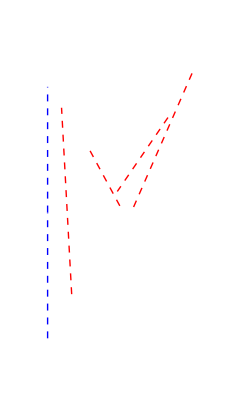

```mathematica
ostrack = ParametricPlot[{ospos[t]},{t,0,totaltime},Axes->False,PlotStyle->Directive[Dashed,Blue,Thick],PlotRange->{{-1,7},{-1,12}}];
r1r2track[{vr0_,vr1_}]:=ParametricPlot[{trialpos[brg0,brg[targetpos[totaltime]-ospos[totaltime]],vr0,vr1,ospos[0],ospos[totaltime],t,totaltime]},{t,0,totaltime},Axes->False,PlotStyle->Directive[Dashed,Red,Thick]];
overlayedtracks=Show[{ostrack}~Join~Table[r1r2track[i],{i,r1r2list}]]
```

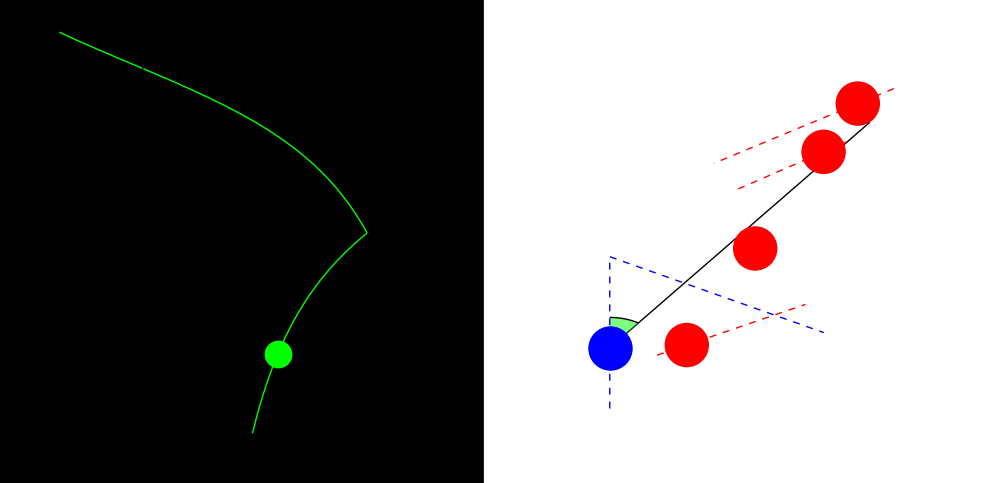

```mathematica
multitrackanimation[t_]:=GraphicsGrid[{{
Show[
screen,
Graphics[{
Green,
PointSize[.05],
Point[{brg[trialpos[brg0,brg[targetpos[totaltime]-ospos[totaltime]],r0,r1,ospos[0],ospos[totaltime],t,totaltime]-ospos[t]]*180/π,t}]
},ImageSize->Large]
],
Show[
Graphics[{
Line[{ospos[t],trialpos[brg0,brg[targetpos[totaltime]-ospos[totaltime]],r0,r1,ospos[0],ospos[totaltime],t,totaltime]}],
Opacity[.5],
Green,
Disk[ospos[t],1,{π/2,π/2-brg[trialpos[brg0,brg[targetpos[totaltime]-ospos[totaltime]],r0,r1,ospos[0],ospos[totaltime],t,totaltime]-ospos[t]]}],
Opacity[1],
Black,
Circle[ospos[t],1,{π/2,π/2-brg[trialpos[brg0,brg[targetpos[totaltime]-ospos[totaltime]],r0,r1,ospos[0],ospos[totaltime],t,totaltime]-ospos[t]]}],
PointSize[.08],
Blue,
Point[ospos[t]]
},PlotRange->{{-1,7},{-1,12}}],
Graphics[{Red,PointSize[.08]}~Join~Table[
Point[trialpos[brg0,brg[targetpos[totaltime]-ospos[totaltime]],i[[1]],i[[2]],ospos[0],ospos[totaltime],t,totaltime]],
{i,r1r2list}]
],
overlayedtracks
]
}},ImageSize->1000]
multitrackanimation[2]
```

```mathematica
frames=Table[multitrackanimation[t],{t,0,10,.2}];
```

```mathematica
Export["multitrack.gif",frames,"AnimationRepetitions"->∞]
```

multitrack.gif

```mathematica
pathlist=Table[{trialpos[brg0,brg[targetpos[totaltime]-ospos[totaltime]],i[[1]],i[[2]],ospos[0],ospos[totaltime],0,totaltime],trialpos[brg0,brg[targetpos[totaltime]-ospos[totaltime]],i[[1]],i[[2]],ospos[0],ospos[totaltime],totaltime,totaltime]},{i,r1r2list}];
pathpos[i_,t_]:=(pathlist[[i]][[1]]*(totaltime-t)+pathlist[[i]][[2]]*t)/totaltime;
secondcourse=2π/3;
r0=12;
r1=Norm[targetpos[totaltime]-ospos[totaltime]];
```

Table::iterb: Iterator {i,r1r2list} does not have appropriate bounds.

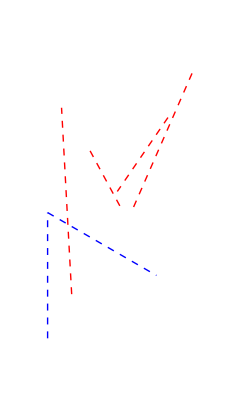

```mathematica
ostrack = ParametricPlot[{ospos[t]},{t,0,totaltime},Axes->False,PlotStyle->Directive[Dashed,Blue,Thick],PlotRange->{{-1,7},{-1,12}}];
trialtracks=ParametricPlot[Table[pathpos[i,t],{i,4}],{t,0,totaltime},PlotStyle->Directive[Dashed,Red,Thick]];
overlayedturntracks=Show[ostrack,trialtracks]
```

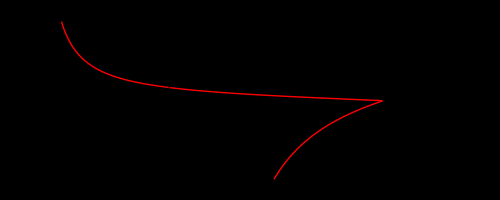
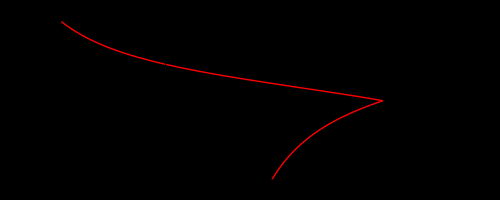
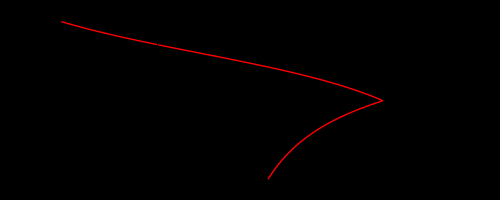

```mathematica
altscreen[i_]:=ParametricPlot[{{brg[pathpos[i,t]-ospos[t]]*180/π,t}},{t,0,totaltime},PlotStyle->Directive[Red,Thin],Ticks->{Range[-180,180,45],Range[0,10,2]},AxesLabel->{"True Bearing (°)","Time (Min)"},AxesStyle->Directive[White,12],AspectRatio->Full,Background->Black];
altscreens=Table[altscreen[i],{i,3}]
```

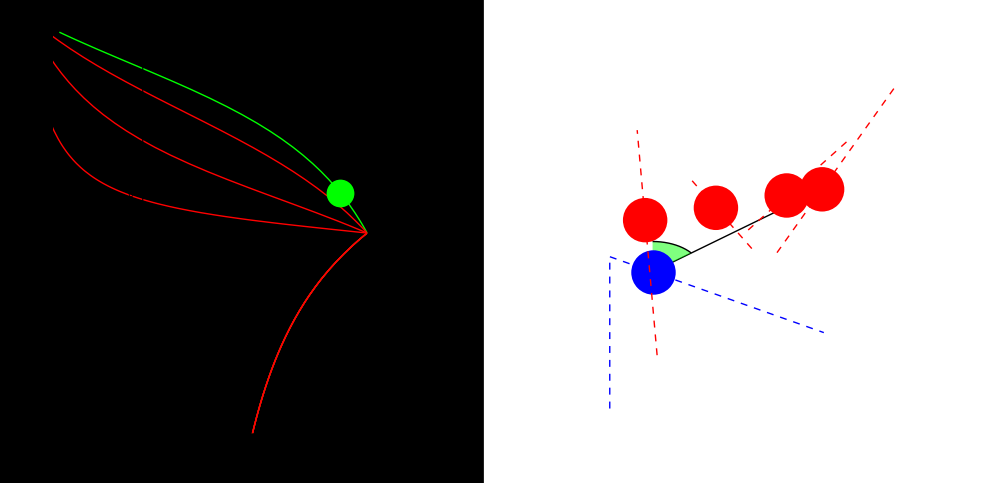

```mathematica
multitrackanimationturn[t_]:=GraphicsGrid[{{
Show[
screen,
altscreens,
Graphics[{
Green,
PointSize[.05],
Point[{brg[targetpos[t]-ospos[t]]*180/π,t}]
},ImageSize->Large]
],
Show[
Graphics[{
Line[{ospos[t],trialpos[brg0,brg[targetpos[totaltime]-ospos[totaltime]],r0,r1,ospos[0],ospos[totaltime],t,totaltime]}],
Opacity[.5],
Green,
Disk[ospos[t],1,{π/2,π/2-brg[trialpos[brg0,brg[targetpos[totaltime]-ospos[totaltime]],r0,r1,ospos[0],ospos[totaltime],t,totaltime]-ospos[t]]}],
Opacity[1],
Black,
Circle[ospos[t],1,{π/2,π/2-brg[trialpos[brg0,brg[targetpos[totaltime]-ospos[totaltime]],r0,r1,ospos[0],ospos[totaltime],t,totaltime]-ospos[t]]}],
PointSize[.08],
Blue,
Point[ospos[t]]
},PlotRange->{{-1,7},{-1,12}}],
Graphics[{Red,PointSize[.08]}~Join~Table[
Point[pathpos[i,t]],{i,4}
]],
overlayedturntracks
]
}},ImageSize->1000]
multitrackanimationturn[6]
```

```mathematica
frames=Table[multitrackanimationturn[t],{t,0,10,.2}];
```

```mathematica
Export["multitrackturn.gif",frames,"AnimationRepetitions"->∞]
```

multitrackturn.gif

```mathematica
secondcourse=2π/3;
timeoftargetzig=3;
targetsecondcourse=-3π/4;
tv0={0,-1.5};
tv1=Norm[tv0]*{Sin[targetsecondcourse],Cos[targetsecondcourse]};
targetpos[t_]:=tp0+If[t<timeoftargetzig,tv0*t,tv0*timeoftargetzig+tv1*(t-timeoftargetzig)];
```